```mathematica
SetDirectory["L:/moose/trunk/wallaby/doc/theory/figures"]
```

L:\moose\trunk\wallaby\doc\theory\figures

```mathematica
v[s_,m_] := Sqrt[s]*(1-(1-s^(1/m))^m)^2
```

```mathematica
cut = 0.99;
mm = 0.3;
vc=v[cut,mm];
vcp=D[v[s,m],s]/.{s->cut, m->mm};
vcpp=D[v[s,m],{s,2}]/.{s->cut, m->mm};
al = (1-vc - vcp(1-cut)-vcpp(1-cut)^2)/(1-cut)^3;
cub[s_] := vc + vcp(s-cut)+vcpp(s-cut)^2+al(s-cut)^3;
vmod[s_,m_] :=If[s<cut,v[s,m],cub[s]];
```

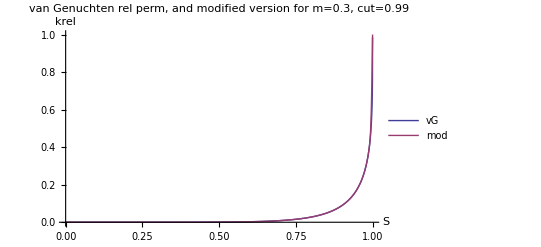

```mathematica
Plot[{v[s,mm],vmod[s,mm]},{s,0,1},AxesLabel->{"S","krel"},PlotLabel->"van Genuchten rel perm, and modified version for m=0.3, cut=0.99",PlotLegends->{"vG","mod"},PlotRange->All]
```

```mathematica
Export["vg_krel_mod_2.eps",%,"EPS"]
```

vg_krel_mod_2.eps